# TT Term Reference Value : D_s,5.02 TeV (2.5, 0.0251)

## v_T=0.3(0.30952),γ_c=0.39,γ_s=0.8,T=0.175(0.16-0.19)

```mathematica
TT[p_,eta_]:=36*Sqrt[p^2+1.96^2]*(5*5.0676896*Pi(9*5.0676896)^2)/(2Pi)^3*2*0.39*0.8*BesselI[0,(p Sinh[eta])/0.175]*NIntegrate[660*(1-x)^9*x^2*BesselK[1,Cosh[eta]/0.175(Sqrt[0.46^2+x^2 p^2]+Sqrt[1.28^2+(1-x)^2 p^2])],{x,0,1}];
```

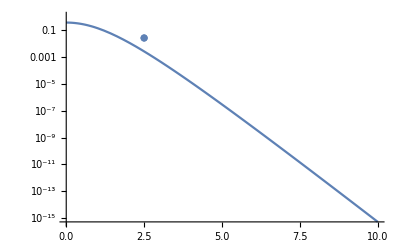

```mathematica
Show[LogPlot[TT[p,ArcTanh[0.3]],{p,0,10}],ListLogPlot[{{2.5,0.0251}}]]
```

```mathematica
(*(2.5,  0.0251) *)
```

```mathematica
TT[2.5,ArcTanh[0.3]]
```

0.00252664

```mathematica
ArcTanh[0.3]
```

0.30952

```mathematica
Ts[p_,eta_]:=12*0.8*Sqrt[p^2+0.46^2]/(2Pi)^3*BesselI[0,(p Sinh[eta])/0.185]*BesselK[1,Cosh[eta]/0.185*Sqrt[p^2+0.46^2]];
Tc[p_,eta_]:=12*0.26*Sqrt[p^2+1.28^2]/(2Pi)^3*BesselI[0,(p Sinh[eta])/0.185]*BesselK[1,Cosh[eta]/0.185*Sqrt[p^2+1.28^2]];
```

```mathematica
Ts[2.5,ArcTanh[0.2]]
```

1.10369×10^-7

```mathematica
Tc[2.5,ArcTanh[0.3]]
```

1.95346×10^-8

```mathematica
ArcTanh[0.3]
```

0.30952